```mathematica
$Assumptions = {r+gkw>gw, w>0, k>0,r>0,D>0, τ>0,g>0,i>0,j>0}
```

{gkw+r>gw,w>0,k>0,r>0,D>0,τ>0,g>0,i>0,j>0}

```mathematica
A=w {{1,-k}, {1,-k}};
(*J=A Exp[γ];*)
J=A g
F = {{-r, 0 }, {0, -r}}+J;
```

{{g w,-g k w},{g w,-g k w}}

## Stationary solution - Reduced model

### Stationary average

```mathematica
(*Define the system of differential equations*)
system={
τ x1'[t]==F[[1,1]]*x1[t]+F[[1,2]]*x2[t]+hE,
τ x2'[t]==F[[2,1]]*x1[t]+F[[2,2]]*x2[t]+hI
};
(*Define the initial condition*)
initialCondition={x1[0]==0,x2[0]==0};
(*Solve the system*)
solution=DSolve[Join[system,initialCondition],{x1[t],x2[t]},t];
meanTimeDep={x1[t]/.solution[[1,1]], x2[t]/.solution[[1,2]]}//FullSimplify
```

{(ⅇ^(-(t (r+g k w))/τ) (ⅇ^((g t w)/τ) (hE-hI k) r-ⅇ^((g k t w)/τ) (hE-hI) k (r+g (-1+k) w)+ⅇ^((t (r+g k w))/τ) (-1+k) (hE r+g (hE-hI) k w)))/((-1+k) r (r+g (-1+k) w)),(ⅇ^(-(t (r+g k w))/τ) (ⅇ^((g t w)/τ) (hE-hI k) r+ⅇ^((t (r+g k w))/τ) (-1+k) (hI r+g (hE-hI) w)-ⅇ^((g k t w)/τ) (hE-hI) (r+g (-1+k) w)))/((-1+k) r (r+g (-1+k) w))}

```mathematica
meanSt = Limit[meanTimeDep,t->Infinity]
```

{ConditionalExpression[(hE r+g (hE-hI) k w)/(r (r+g (-1+k) w)), ],ConditionalExpression[(hI r+g (hE-hI) w)/(r (r+g (-1+k) w)), ]}

```mathematica
meanSt={(hE r+g (hE-hI) k w)/(r (r+g (-1+k) w)),(hI r+g (hE-hI) w)/(r (r+g (-1+k) w))}
```

{(hE r+g (hE-hI) k w)/(r (r+g (-1+k) w)),(hI r+g (hE-hI) w)/(r (r+g (-1+k) w))}

### Stationary covariance matrix from Lyapunov equation

```mathematica
sigma = {{a11, a12}, {a21,a22}};
eye = {{1,0},{0,1}};
sol = Solve[{F.sigma + sigma.(Transpose[F])==-2d eye}, {a11,a12,a21,a22}][[1]];
sigmaSt= sigma /. sol;
sigmaSt =sigmaSt//FullSimplify;
sigmaSt // MatrixForm
```

((d (2 r^2+g (-1+3 k) r w+2 g^2 k^2 w^2))/(r (r+g (-1+k) w) (2 r+g (-1+k) w)) | (d g w (r-k r+2 g k w))/(r (r+g (-1+k) w) (2 r+g (-1+k) w))
(d g w (r-k r+2 g k w))/(r (r+g (-1+k) w) (2 r+g (-1+k) w)) | (d (2 r^2+g (-3+k) r w+2 g^2 w^2))/(r (r+g (-1+k) w) (2 r+g (-1+k) w)))

## Self-consistent equation for plasticity

### Hebbian plasticity

```mathematica
gamma1 =p*(sigmaSt[[1,2]])//FullSimplify;
gamma2=p*(meanSt[[1]]*meanSt[[2]] )//FullSimplify;
gamma = gamma1 + gamma2;
gamma =gamma/.{g->Exp[γ]}
```

(d ⅇ^γ p w (r-k r+2 ⅇ^γ k w))/(r (r+ⅇ^γ (-1+k) w) (2 r+ⅇ^γ (-1+k) w))+(p (hI r+ⅇ^γ (hE-hI) w) (hE r+ⅇ^γ (hE-hI) k w))/(r^2 (r+ⅇ^γ (-1+k) w)^2)

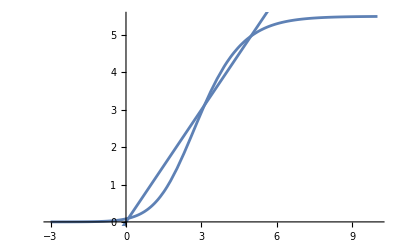

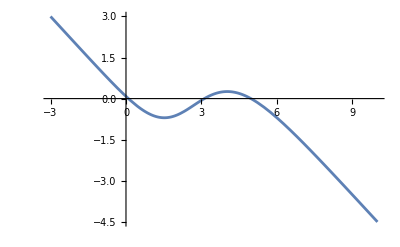

```mathematica
Show[{Plot[(gamma)/.{k->1.1,w->2,r->1,d->1,hE->0,hI->0,p->0.025},{γ,-3,10}],Plot[γ,{γ,-3,10}]}]
Plot[(gamma-γ)/.{k->1.1,w->2,r->1,d->1,hE->0,hI->0,p->0.025},{γ,-3,10}]
```

#### Potential

```mathematica
Ugamma=Integrate[-γ+gamma,γ]//FullSimplify
```

(2 hE hI p Log[ⅇ^γ]+(r ((2 (hE-hI k)^2 p)/(r+ⅇ^γ (-1+k) w)-(-1+k)^2 r γ^2)+2 p ((hE^2 k+hI^2 k-hE hI (1+k^2)-d (1+k^2) r) Log[r+ⅇ^γ (-1+k) w]+d (1+k)^2 r Log[2 r+ⅇ^γ (-1+k) w]))/(-1+k)^2)/(2 r^2)

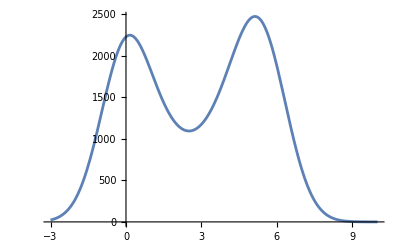

```mathematica
Plot[Exp[Ugamma]/.{r->1,w->2.5,k->1.1,d->1,hE->0,hI->0,p->0.025},{γ,-3,10},PlotRange->All]
```

### With Oja rule

```mathematica
den = (λ+sigmaSt[[1,1]] + sigmaSt[[2,2]] +meanSt[[1]]^2+meanSt[[2]]^2 )//FullSimplify
gamma1 =p*(sigmaSt[[1,2]]/den)//FullSimplify
gamma2=p*(meanSt[[1]]*meanSt[[2]] /den)//FullSimplify
gamma = gamma1 + gamma2;
gamma =gamma/.{g->Exp[γ]}
```

1/(r^2 (r+g (-1+k) w)^2 (2 r+g (-1+k) w))(2 r^3 (hE^2+hI^2+2 d r)+g r^2 (hI^2 (-5+k)-4 hE hI (-1+k)+hE^2 (-1+5 k)+8 d (-1+k) r) w+2 g^2 r ((hE-hI) (hE+hE k (-1+2 k)+hI (-2+k-k^2))+d (3+k (-4+3 k)) r) w^2+g^3 (-1+k) (1+k^2) ((hE-hI)^2+2 d r) w^3)+λ

(d g p w (r-k r+2 g k w))/(r (r+g (-1+k) w) (2 r+g (-1+k) w) ((2 r^3 (hE^2+hI^2+2 d r)+g r^2 (hI^2 (-5+k)-4 hE hI (-1+k)+hE^2 (-1+5 k)+8 d (-1+k) r) w+2 g^2 r ((hE-hI) (hE+hE k (-1+2 k)+hI (-2+k-k^2))+d (3+k (-4+3 k)) r) w^2+g^3 (-1+k) (1+k^2) ((hE-hI)^2+2 d r) w^3)/(r^2 (r+g (-1+k) w)^2 (2 r+g (-1+k) w))+λ))

(p (hI r+g (hE-hI) w) (hE r+g (hE-hI) k w))/(r^2 (r+g (-1+k) w)^2 ((2 r^3 (hE^2+hI^2+2 d r)+g r^2 (hI^2 (-5+k)-4 hE hI (-1+k)+hE^2 (-1+5 k)+8 d (-1+k) r) w+2 g^2 r ((hE-hI) (hE+hE k (-1+2 k)+hI (-2+k-k^2))+d (3+k (-4+3 k)) r) w^2+g^3 (-1+k) (1+k^2) ((hE-hI)^2+2 d r) w^3)/(r^2 (r+g (-1+k) w)^2 (2 r+g (-1+k) w))+λ))

(d ⅇ^γ p w (r-k r+2 ⅇ^γ k w))/(r (r+ⅇ^γ (-1+k) w) (2 r+ⅇ^γ (-1+k) w) ((2 r^3 (hE^2+hI^2+2 d r)+ⅇ^γ r^2 (hI^2 (-5+k)-4 hE hI (-1+k)+hE^2 (-1+5 k)+8 d (-1+k) r) w+2 ⅇ^(2 γ) r ((hE-hI) (hE+hE k (-1+2 k)+hI (-2+k-k^2))+d (3+k (-4+3 k)) r) w^2+ⅇ^(3 γ) (-1+k) (1+k^2) ((hE-hI)^2+2 d r) w^3)/(r^2 (r+ⅇ^γ (-1+k) w)^2 (2 r+ⅇ^γ (-1+k) w))+λ))+(p (hI r+ⅇ^γ (hE-hI) w) (hE r+ⅇ^γ (hE-hI) k w))/(r^2 (r+ⅇ^γ (-1+k) w)^2 ((2 r^3 (hE^2+hI^2+2 d r)+ⅇ^γ r^2 (hI^2 (-5+k)-4 hE hI (-1+k)+hE^2 (-1+5 k)+8 d (-1+k) r) w+2 ⅇ^(2 γ) r ((hE-hI) (hE+hE k (-1+2 k)+hI (-2+k-k^2))+d (3+k (-4+3 k)) r) w^2+ⅇ^(3 γ) (-1+k) (1+k^2) ((hE-hI)^2+2 d r) w^3)/(r^2 (r+ⅇ^γ (-1+k) w)^2 (2 r+ⅇ^γ (-1+k) w))+λ))

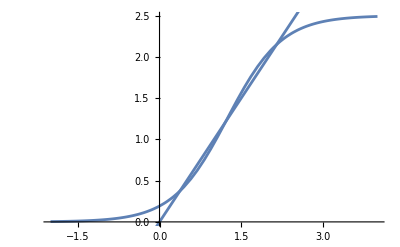

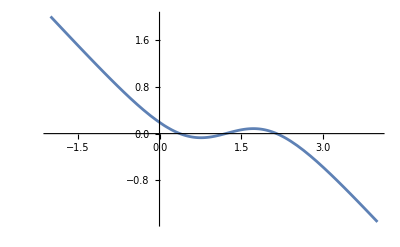

```mathematica
Show[{Plot[(gamma)/.{k->1.,w->2,r->4,d->1,hE->0,hI->0,p->5.,λ->1},{γ,-2,4}],Plot[γ,{γ,-2,4}]}]
Plot[(gamma-γ)/.{k->1.,w->2,r->4,d->1,hE->0,hI->0,p->5.,λ->1},{γ,-2,4}]
```

#### Potential

```mathematica
Ugamma=Integrate[-γ+gamma,γ]//FullSimplify
```

-((γ (hE^2+hI^2+2 d r+r^2 λ) (((hE-hI)^2+2 d r) (-2 k p+γ+k^2 γ)+(-1+k)^2 r^2 γ λ)+2 p (hE^2 k-hE hI (1+k^2)+k (hI^2+2 d r)) ((hE-hI)^2+r (2 d+r λ)) Log[ⅇ^γ]+2 p ((1+k^2) ((hE-hI)^2+2 d r)+(-1+k)^2 r^2 λ) ((hE-hI)^2+r (2 d+r λ)) RootSum[2 hE^2 r^3+2 hI^2 r^3+4 d r^4+2 r^5 λ-hE^2 r^2 w #1+4 hE hI r^2 w #1-5 hI^2 r^2 w #1+5 hE^2 k r^2 w #1-4 hE hI k r^2 w #1+hI^2 k r^2 w #1-8 d r^3 w #1+8 d k r^3 w #1-5 r^4 w λ #1+5 k r^4 w λ #1+2 hE^2 r w^2 #1^2-6 hE hI r w^2 #1^2+4 hI^2 r w^2 #1^2-2 hE^2 k r w^2 #1^2+4 hE hI k r w^2 #1^2-2 hI^2 k r w^2 #1^2+4 hE^2 k^2 r w^2 #1^2-6 hE hI k^2 r w^2 #1^2+2 hI^2 k^2 r w^2 #1^2+6 d r^2 w^2 #1^2-8 d k r^2 w^2 #1^2+6 d k^2 r^2 w^2 #1^2+4 r^3 w^2 λ #1^2-8 k r^3 w^2 λ #1^2+4 k^2 r^3 w^2 λ #1^2-hE^2 w^3 #1^3+2 hE hI w^3 #1^3-hI^2 w^3 #1^3+hE^2 k w^3 #1^3-2 hE hI k w^3 #1^3+hI^2 k w^3 #1^3-hE^2 k^2 w^3 #1^3+2 hE hI k^2 w^3 #1^3-hI^2 k^2 w^3 #1^3+hE^2 k^3 w^3 #1^3-2 hE hI k^3 w^3 #1^3+hI^2 k^3 w^3 #1^3-2 d r w^3 #1^3+2 d k r w^3 #1^3-2 d k^2 r w^3 #1^3+2 d k^3 r w^3 #1^3-r^2 w^3 λ #1^3+3 k r^2 w^3 λ #1^3-3 k^2 r^2 w^3 λ #1^3+k^3 r^2 w^3 λ #1^3&,(-2 hE^2 r^2 Log[ⅇ^γ-#1]-2 hE hI r^2 Log[ⅇ^γ-#1]+2 hE hI k r^2 Log[ⅇ^γ-#1]+2 hI^2 k r^2 Log[ⅇ^γ-#1]-d r^3 Log[ⅇ^γ-#1]+d k r^3 Log[ⅇ^γ-#1]+hE^2 r w Log[ⅇ^γ-#1] #1+3 hE hI r w Log[ⅇ^γ-#1] #1-3 hE^2 k r w Log[ⅇ^γ-#1] #1-2 hE hI k r w Log[ⅇ^γ-#1] #1-3 hI^2 k r w Log[ⅇ^γ-#1] #1+3 hE hI k^2 r w Log[ⅇ^γ-#1] #1+hI^2 k^2 r w Log[ⅇ^γ-#1] #1+d r^2 w Log[ⅇ^γ-#1] #1-4 d k r^2 w Log[ⅇ^γ-#1] #1+d k^2 r^2 w Log[ⅇ^γ-#1] #1-hE hI w^2 Log[ⅇ^γ-#1] #1^2+hE^2 k w^2 Log[ⅇ^γ-#1] #1^2+hE hI k w^2 Log[ⅇ^γ-#1] #1^2+hI^2 k w^2 Log[ⅇ^γ-#1] #1^2-hE^2 k^2 w^2 Log[ⅇ^γ-#1] #1^2-hE hI k^2 w^2 Log[ⅇ^γ-#1] #1^2-hI^2 k^2 w^2 Log[ⅇ^γ-#1] #1^2+hE hI k^3 w^2 Log[ⅇ^γ-#1] #1^2+2 d k r w^2 Log[ⅇ^γ-#1] #1^2-2 d k^2 r w^2 Log[ⅇ^γ-#1] #1^2)/(-hE^2 r^2+4 hE hI r^2-5 hI^2 r^2+5 hE^2 k r^2-4 hE hI k r^2+hI^2 k r^2-8 d r^3+8 d k r^3-5 r^4 λ+5 k r^4 λ+4 hE^2 r w #1-12 hE hI r w #1+8 hI^2 r w #1-4 hE^2 k r w #1+8 hE hI k r w #1-4 hI^2 k r w #1+8 hE^2 k^2 r w #1-12 hE hI k^2 r w #1+4 hI^2 k^2 r w #1+12 d r^2 w #1-16 d k r^2 w #1+12 d k^2 r^2 w #1+8 r^3 w λ #1-16 k r^3 w λ #1+8 k^2 r^3 w λ #1-3 hE^2 w^2 #1^2+6 hE hI w^2 #1^2-3 hI^2 w^2 #1^2+3 hE^2 k w^2 #1^2-6 hE hI k w^2 #1^2+3 hI^2 k w^2 #1^2-3 hE^2 k^2 w^2 #1^2+6 hE hI k^2 w^2 #1^2-3 hI^2 k^2 w^2 #1^2+3 hE^2 k^3 w^2 #1^2-6 hE hI k^3 w^2 #1^2+3 hI^2 k^3 w^2 #1^2-6 d r w^2 #1^2+6 d k r w^2 #1^2-6 d k^2 r w^2 #1^2+6 d k^3 r w^2 #1^2-3 r^2 w^2 λ #1^2+9 k r^2 w^2 λ #1^2-9 k^2 r^2 w^2 λ #1^2+3 k^3 r^2 w^2 λ #1^2)&])/(2 ((1+k^2) ((hE-hI)^2+2 d r)+(-1+k)^2 r^2 λ) (hE^2+hI^2+r (2 d+r λ))))

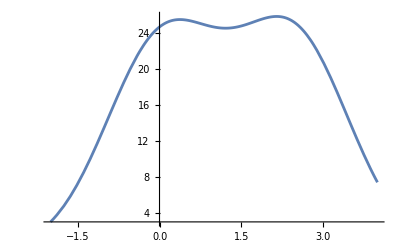

```mathematica
Plot[Exp[Ugamma]/.{k->1.,w->2,r->4,d->1,hE->0,hI->0,p->5.,λ->1},{γ,-2,4},PlotRange->All]
```

## Bounds mutual information

Define network variables

```mathematica
xe[h_,g_] := Evaluate[meanSt[[1]]]
xi[h_,g_]:= Evaluate[meanSt[[2]]]
x[h_,g_]:= {xe[h,g],xi[h,g]};

Cov[g_]:=Evaluate[sigmaSt];
```

Define pairwise distances

```mathematica
ch[x1_,x2_,cov1_,cov2_]:=1/8 Transpose[x1-x2].Inverse[cov2].(x1-x2);
kl[x1_,x2_,cov1_,cov2_]:=1/2 ( Transpose[x1-x2].Inverse[cov2].(x1-x2) + Tr[Inverse[cov2].cov1]-Log[Det[cov1]/Det[cov2]]-2);
```

```mathematica
kl[x[0,g1],x[h2,g2],Cov[g1],Cov[g2]]//FullSimplify
```

ConditionalExpression[1/4 ((h2^2 (2 r+g2 (-1+k) w) (2 r^2+g2 (-1+3 k) r w+g2^2 (1+k^2) w^2))/(D r (r+g2 (-1+k) w) (2 r^2+2 g2 (-1+k) r w+g2^2 (1+k^2) w^2))-(2 (g1-g2) w (4 (-1+k) r^3+4 (g2 (-1+k)^2-2 g1 k) r^2 w+2 g2 (-1+k) (g2-4 g1 k+g2 k^2) r w^2+g1 g2^2 (-1+k)^2 (1+k^2) w^3))/((r+g1 (-1+k) w) (2 r+g1 (-1+k) w) (2 r^2+2 g2 (-1+k) r w+g2^2 (1+k^2) w^2))+2 Log[r+g1 (-1+k) w]-2 Log[((r+g2 (-1+k) w) (2 r+g2 (-1+k) w)^2 (2 r^2+2 g1 (-1+k) r w+g1^2 (1+k^2) w^2))/((2 r+g1 (-1+k) w)^2 (2 r^2+2 g2 (-1+k) r w+g2^2 (1+k^2) w^2))]), h2∈ℝ&&k>1&&r+g1 k w>g1 w&&r+g2 k w>g2 w]

```mathematica
kl[x[i dh,g1],x[j dh,g2],Cov[g1],Cov[g2]]//FullSimplify
```

ConditionalExpression[1/4 ((-2 D (g1-g2) r w (r+g1 (-1+k) w) (r+g2 (-1+k) w) (4 (-1+k) r^3+4 (g2-2 (g1+g2) k+g2 k^2) r^2 w+2 g2 (-1+k) (g2-4 g1 k+g2 k^2) r w^2+g1 g2^2 (-1+k)^2 (1+k^2) w^3)+dh^2 (2 r+g1 (-1+k) w) (2 r+g2 (-1+k) w) (-2 i j (r+g1 (-1+k) w) (r+g2 (-1+k) w) (2 r^2+(g2 (-1+k)+2 g1 k) r w+g1 g2 (1+k^2) w^2)+j^2 (r+g1 (-1+k) w)^2 (2 r^2+g2 (-1+3 k) r w+g2^2 (1+k^2) w^2)+i^2 (r+g2 (-1+k) w) (2 r^3+(g2 (-3+k)+4 g1 k) r^2 w+2 (g2^2+g1 g2 (-1+(-2+k) k)+g1^2 (1+k^2)) r w^2+g1^2 g2 (-1+k) (1+k^2) w^3)))/(D r (r+g1 (-1+k) w)^2 (2 r+g1 (-1+k) w) (r+g2 (-1+k) w) (2 r^2+2 g2 (-1+k) r w+g2^2 (1+k^2) w^2))-2 Log[((r+g2 (-1+k) w) (2 r+g2 (-1+k) w)^2 (2 r^2+2 g1 (-1+k) r w+g1^2 (1+k^2) w^2))/((r+g1 (-1+k) w) (2 r+g1 (-1+k) w)^2 (2 r^2+2 g2 (-1+k) r w+g2^2 (1+k^2) w^2))]), dh∈ℝ&&k>1&&r+g1 k w>g1 w&&r+g2 k w>g2 w]

```mathematica
kl[x[i dh,g],x[j dh,g],Cov[g],Cov[g]]//FullSimplify
```

ConditionalExpression[(dh^2 (i-j)^2 (2 r+g (-1+k) w) (2 r^2+g (-1+3 k) r w+g^2 (1+k^2) w^2))/(4 D r (r+g (-1+k) w) (2 r^2+2 g (-1+k) r w+g^2 (1+k^2) w^2)), dh∈ℝ&&k>1]